```mathematica
Forecasting Stock Prices: Caterpillar - NYSE:CAT
```

```mathematica
Functions
```

```mathematica
smoothData[list, n, r]: 
  list - list of numbers to be smoothed
  n - length of Daubechies filter (2n coefficients)
  r - number of iterations of wavelet transform
  
Smooths a list by applying universal thresholding to all levels of a 
Daubechies filter decomposition.  Universal Thresholding is the default 
for WaveletThreshold[ ].  StationaryWaveletTransform[ ] "wraps" 
coeffiecients at the begining (top) of the transform.  This is preferable 
for forecasting, since we are trying to extrapolate off the end of our data set.
```

```mathematica
smoothData[list_,n_,r_]:= InverseWaveletTransform[WaveletThreshold[StationaryWaveletTransform[list,DaubechiesWavelet[n],r]]]
```

```mathematica
sample[list, n, r] : 
   list - list of numbers to extract sample from
   n - starting position in list
   r - lookback.  Number of elements to sample
```

```mathematica
sample[list_, n_, r_]:=list[[n-r;;n]]
```

```mathematica
forecast[data, τ, filter, levels] : 
   data - list of numbers to extract sample from
   n - starting position in list
   r - number of points to sample.  i.e. stop at position r - 1 in list.
```

```mathematica
forecast[data_,τ_,filter_,levels_]:=((* Compute nondecimated (stationary) wavelet transform *)
swt=StationaryWaveletTransform[data,filter,levels];
(* Get the coefficients *)
swtCoef=swt[Automatic];
(* Extrapolate each level *)
Do[
swtCoef[[i,2]]=ArrayPad[swtCoef[[i,2]],{0,τ},"Extrapolated",InterpolationOrder->1],
{i,1,levels+1}
];
(* Invert and take the last value *)Last[InverseWaveletTransform[DiscreteWaveletData[swtCoef,filter]]]
)
```

```mathematica
Code
```

Read ticker prices from file

```mathematica
tkrPrices = ReadList["C:\\Users\\John\\Desktop\\Wavelets-Economics\\cat.txt"];
(* Length[tkrPrices] *)
(* Create list to hold predictions *)
prediction = Table[0,{Length[tkrPrices]}];
```

```mathematica
Do[
priceSample = sample[tkrPrices, i, 600];
(* smoothSample = smoothData[priceSample, 1, 2]; *)
prediction[[i]] = forecast[priceSample, 1, DaubechiesWavelet[1], 1]
,{i, 1501, 1621}
]
Export["C:\\Users\\John\\Desktop\\Wavelets-Economics\\tmp.txt", prediction, "List"]
```

Part::span: -600 + i ;; i is not a valid Span specification. A Span specification should be 1, 2, or 3 integers separated by ;;. (Any of the integers can be omitted or replaced with All.)

```mathematica
prediction[[3200]]
tkrPrices[[3200]]
```

295.745

297.42

```mathematica
ListPlot[{smoothSample1, smoothSample2, smoothSample3}, Joined -> True]
```

```mathematica
Export["C:\\Users\\John\\Desktop\\Wavelets-Economics\\tmp.txt", prediction, "List"]
```

```mathematica
(********************* TEST CODE ************************)
tkrPrices = ReadList["C:\\Users\\John\\Desktop\\Wavelets-Economics\\cat.txt"];
priceSample = sample[tkrPrices, 12000, 600];
```

```mathematica
smoothSample = smoothData[priceSample, 1, 2];
```

```mathematica
swt = StationaryWaveletTransform[smoothSample, DaubechiesWavelet[2], 3];
```

```mathematica
swtCoef=swt[Automatic]
```

```mathematica
Length[swtCoef[[1,2]]]
```

601

```mathematica
fdct = FourierDCT[Part[swtCoef[[1,2]],420;;601]];
```

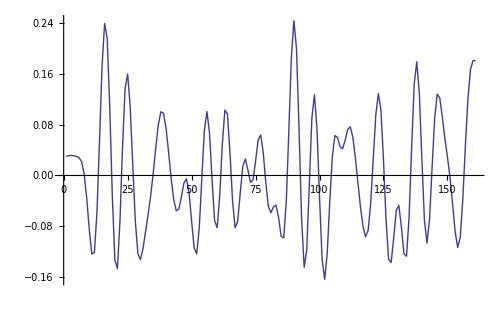

```mathematica
ListLinePlot[FourierDCT[PadRight[Take[fdct,50],161,0],3]]
```

```mathematica
ListLinePlot[fdct]
```

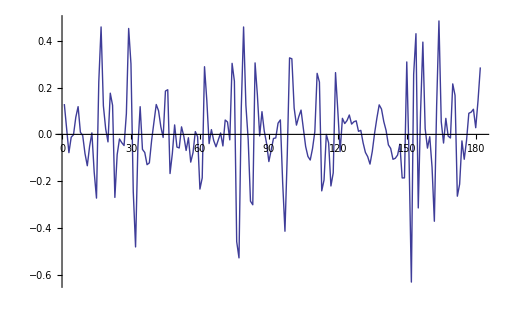

```mathematica
ListLinePlot[Part[swtCoef[[1,2]],420;;601], PlotRange -> All]
```

```mathematica
WaveletListPlot[dwt, Ticks -> Full, PlotRange -> {{430,600}}, AspectRatio -> 2]
```

-Graphics-

```mathematica
ListPlot[Part[swtCoef[[1, 2]], 12000;;12500]]
```

```mathematica
ListPlot[ smoothData ]
```

```mathematica
data1 = {1,2,3,4,5,6,7,8}
```

```mathematica
Length[data1]
```

```mathematica
dwt = StationaryWaveletTransform[data1, DaubechiesWavelet[1], 1]
```

```mathematica
WaveletListPlot[dwt, PlotLayout -> "CommonYAxis"]
```